```mathematica
$Assumptions={τ>0,τR>0,t>=0,τ-t>=0};
```

```mathematica
Psi[t_]=BesselJ[0,t/τR];
dPsi[t_]=D[Psi[t],t];
ddPsi[t_]=D[dPsi[t],t];
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}];
c1=SeriesCoefficient[f[s],{s,0,1}];
```

```mathematica
Clear[τR];

g[t_]=(t+τR)/(τ+2τR);

gs[t_]=c0(DiracDelta[t]-DiracDelta[τ-t])/(τ+2τR);

gs2[t_]=c1(DiracDelta'[t]-DiracDelta'[τ-t])/(τ+2τR);
```

```mathematica
Ws[τ_]=Expand[Psi[0]/2+Integrate[dPsi[τ-t](g[t]+gs[t]),{t,0,τ}]-Integrate[ddPsi[t-u](g[t]+gs[t])(g[u]+gs[u]),{t,0,τ},{u,0,t}]/.HeavisideTheta[0]->1/2]

Ws2[τ_]=Expand[Psi[0]/2+Integrate[dPsi[τ-t](g[t]+gs[t]+gs2[t]),{t,0,τ}]-Integrate[ddPsi[t-u](g[t]+gs[t]+gs2[t])(g[u]+gs[u]+gs2[u]),{t,0,τ},{u,0,t}]/.{HeavisideTheta[0]->1/2,HeavisideTheta[0,τ]->0}]
```

1/2+τ^2/(2 (τ+2 τR)^2)+(τ τR)/(τ+2 τR)^2+τR^2/(2 (τ+2 τR)^2)-τ/(τ+2 τR)-τR/(τ+2 τR)-(τ τR BesselJ[0,τ/τR])/(τ+2 τR)^2-(τR^2 BesselJ[0,τ/τR])/(2 (τ+2 τR)^2)+(τ BesselJ[0,τ/τR])/(τ+2 τR)+(τR BesselJ[0,τ/τR])/(τ+2 τR)-(τ τR BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)+(τR^2 BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)-(τR BesselJ[1,τ/τR])/(2 (τ+2 τR))+(τ^3 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2 (τ+2 τR))

1/2+τ^2/(2 (τ+2 τR)^2)+(τ τR)/(τ+2 τR)^2+τR^2/(4 (τ+2 τR)^2)-τ/(τ+2 τR)-τR/(τ+2 τR)-(3 τ τR BesselJ[0,τ/τR])/(4 (τ+2 τR)^2)-(τR^2 BesselJ[0,τ/τR])/(4 (τ+2 τR)^2)+(τ BesselJ[0,τ/τR])/(τ+2 τR)+(τR BesselJ[0,τ/τR])/(τ+2 τR)-(τ τR BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)-(τR BesselJ[1,τ/τR])/(2 (τ+2 τR))+(τ^3 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2 (τ+2 τR))+(τ^2 HypergeometricPFQ[{1,1},{2,2,2},-τ^2/(4 τR^2)])/(16 (τ+2 τR)^2)-(τ^2 HypergeometricPFQ[{1,1},{2,2,3},-τ^2/(4 τR^2)])/(32 (τ+2 τR)^2)

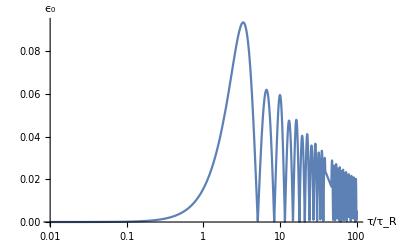

```mathematica
ϵ1[τ_]=Abs[1-Ws[τ]/Ws2[τ]];

τR=1;
LogLinearPlot[ϵ1[τ],{τ,0.01,100},AxesLabel->{"τ/τ_R","ϵ_0"}]
Clear[τR]
```